```mathematica
χ[{L1_,L2_},r_][k_]:=Module[{},
If[r==1,
Return[HeavisideTheta[k-1/2]-HeavisideTheta[k-L1-1/2],Module];
];
If[r==2,
Return[HeavisideTheta[k-L1-1/2]-HeavisideTheta[k-L1-L2-1/2],Module];
];
];
```

```mathematica
J[{L1_,L2_},{p1_,p2_}][k_]:=Outer[Times, {(L2 p1- L1 p2)/(L1+L2)}//Flatten,((χ[{L1,L2},1][k])/L1-(χ[{L1,L2},2][k])/L2)]
```

```mathematica
RedJ[{L1_,L2_},{p1_,p2_}][k_]:=Outer[Times, {(L2 p1- L1 p2)/(L1+L2)}//Flatten,{((χ[{L1,L2},1][k])/L1-(χ[{L1,L2},2][k])/L2+1/L2)}//Flatten]
```

```mathematica
Jvector[{L1_,L2_},{p1_,p2_}]:=J[{L1,L2},{p1,p2}][Range[1,L1+L2]]
```

```mathematica
RedJvector[{L1_,L2_},{p1_,p2_}]:=RedJ[{L1,L2},{p1,p2}][Range[1,L1+L2-1]]
```

```mathematica
Mkernelfunc[L_,x_]:=(-Sin[Pi/L](*+(-1)^x(Cos[Pi/L]-Exp[2Pi I *x/L])*))/(Cos[Pi/L]-Cos[2Pi x/L])
```

```mathematica
MMatrix[{L1_,L2_}]:=Module[{Mkernel,Mkernel1,Mkernel2,k1,k2,M,L=L1+L2},
Mkernel=Table[Mkernelfunc[L,x],{x,0,L-1}];
Mkernel1=Table[Mkernelfunc[L1,x],{x,0,L1-1}];
Mkernel2=Table[Mkernelfunc[L2,x],{x,0,L2-1}];
k1=Table[k*χ[{L1,L2},1][k],{k,1,L}];
k2=Table[(k-L1)*χ[{L1,L2},2][k],{k,1,L}];

M=Table[
(*multiply by Pi to kill exponential scaling of det*)
Pi(1/(Pi*L)Mkernel[[Mod[k-l,L]+1]]+(χ[{L1,L2},1][k]χ[{L1,L2},1][l])/(Pi*L1)Mkernel1[[Mod[k1[[k]]-k1[[l]],L1]+1]]+(χ[{L1,L2},2][k]χ[{L1,L2},2][l])/(Pi*L2)Mkernel2[[Mod[k2[[k]]-k2[[l]],L2]+1]])
,{k,1,L},
{l,1,L}];
Return[M,Module];
];
```

```mathematica
prec=15;
MMatrixN[{L1_,L2_}]:=Module[{Mkernel,Mkernel1,Mkernel2,k1,k2,M,L=L1+L2},
Mkernel=Table[N[Mkernelfunc[L,x],prec],{x,0,L-1}];
Mkernel1=Table[N[Mkernelfunc[L1,x],prec],{x,0,L1-1}];
Mkernel2=Table[N[Mkernelfunc[L2,x],prec],{x,0,L2-1}];
k1=Table[k*χ[{L1,L2},1][k],{k,1,L}];
k2=Table[(k-L1)*χ[{L1,L2},2][k],{k,1,L}];

M=Table[
(*multiply by Pi to kill exponential scaling of det*)
Pi*N[1/(Pi*L)Mkernel[[Mod[k-l,L]+1]]+(χ[{L1,L2},1][k]χ[{L1,L2},1][l])/(Pi*L1)Mkernel1[[Mod[k1[[k]]-k1[[l]],L1]+1]]+(χ[{L1,L2},2][k]χ[{L1,L2},2][l])/(Pi*L2)Mkernel2[[Mod[k2[[k]]-k2[[l]],L2]+1]],prec]
,{k,1,L},
{l,1,L}];
Return[M,Module];
];
```

```mathematica
RedMMatrixN[{L1_,L2_}]:=Module[{Mkernel,Mkernel1,Mkernel2,LastRow,k1,k2,M,L=L1+L2},
Mkernel=Table[N[Mkernelfunc[L,x],prec],{x,0,L-1}];
Mkernel1=Table[N[Mkernelfunc[L1,x],prec],{x,0,L1-1}];
Mkernel2=Table[N[Mkernelfunc[L2,x],prec],{x,0,L2-1}];
k1=Table[k*χ[{L1,L2},1][k],{k,1,L}];
k2=Table[(k-L1)*χ[{L1,L2},2][k],{k,1,L}];
LastRow=Table[Pi*N[1/(Pi*L)Mkernel[[Mod[k-L,L]+1]]+(χ[{L1,L2},1][k]χ[{L1,L2},1][L])/(Pi*L1)Mkernel1[[Mod[k1[[k]]-k1[[L]],L1]+1]]+(χ[{L1,L2},2][k]χ[{L1,L2},2][L])/(Pi*L2)Mkernel2[[Mod[k2[[k]]-k2[[L]],L2]+1]],prec],{k,1,L}];
M=Table[
(*multiply by Pi to kill exponential scaling of det*)
Pi*N[1/(Pi*L)Mkernel[[Mod[k-l,L]+1]]+(χ[{L1,L2},1][k]χ[{L1,L2},1][l])/(Pi*L1)Mkernel1[[Mod[k1[[k]]-k1[[l]],L1]+1]]+(χ[{L1,L2},2][k]χ[{L1,L2},2][l])/(Pi*L2)Mkernel2[[Mod[k2[[k]]-k2[[l]],L2]+1]],prec]-LastRow[[k]]-LastRow[[l]]+LastRow[[L]]
,{k,1,L-1},
{l,1,L-1}];
Return[M,Module];
];
```

```mathematica
RedJMJ[{L1_,L2_}]:=Module[{MInv,L=L1+L2},
MInv = Inverse[RedMMatrixN[{L1,L2}]];
Return[1/L^2 Total[Total[MInv[[1;;L1,1;;L1]]]]]
]
```

### Some random tests

```mathematica
Monitor[Table[{2k,RedJMJ[{2k,200-2k}]},{k,1,50}],k]
```

{{2,0.0002022779006551},{4,0.00066171563345778},{6,0.0013218978872708},{8,0.0021498451230951},{10,0.0031212826433785},{12,0.004216703243534},{14,0.0054196687828188},{16,0.0067159095541917},{18,0.0080927850244039},{20,0.0095389335570937},{22,0.011044031112485},{24,0.012598617440543},{26,0.014193966427642},{28,0.015821986609898},{30,0.017475143038664},{32,0.01914639470983},{34,0.020829143622932},{36,0.022517192717363},{38,0.024204710710794},{40,0.025886202391801},{42,0.027556483284628},{44,0.029210657863738},{46,0.030844100683767},{48,0.032452439928899},{50,0.034031542989172},{52,0.035577503749749},{54,0.03708663133948},{56,0.038555440131984},{58,0.039980640829303},{60,0.041359132487411},{62,0.042687995366297},{64,0.043964484506238},{66,0.045186023947278},{68,0.046350201521608},{70,0.047454764158954},{72,0.048497613653811},{74,0.049476802850639},{76,0.050390532209291},{78,0.051237146718181},{80,0.052015133127144},{82,0.052723117475802},{84,0.053359862896573},{86,0.053924267674361},{88,0.05441536354753},{90,0.054832314237018},{92,0.055174414192492},{94,0.055441087546264},{96,0.055631887267349},{98,0.055746494509628},{100,0.055784718149475}}

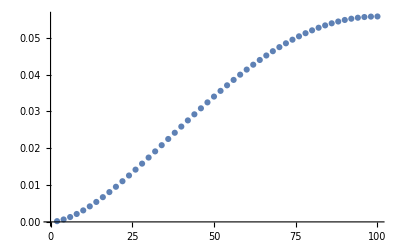

```mathematica
ListPlot[%341]
```

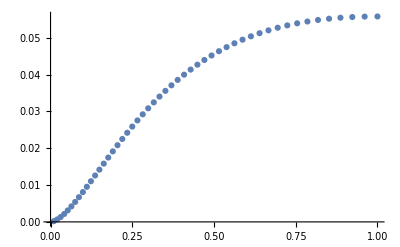

```mathematica
ListPlot[{(#[[1]])/(200-#[[1]]),#[[2]]}&/@%341]
```

```mathematica
Monitor[Table[{2j,Det[Developer`ToPackedArray[RedMMatrixN[{2j,200-2j}],Real]]},{j,1,50}],j]
```

{{2,27366.6},{4,32602.},{6,36080.8},{8,38758.},{10,40960.1},{12,42842.2},{14,44491.4},{16,45961.8},{18,47289.7},{20,48500.5},{22,49613.1},{24,50641.5},{26,51596.8},{28,52487.6},{30,53321.1},{32,54102.9},{34,54837.8},{36,55530.},{38,56182.6},{40,56798.8},{42,57381.},{44,57931.4},{46,58451.9},{48,58944.2},{50,59409.7},{52,59849.7},{54,60265.4},{56,60657.9},{58,61028.1},{60,61376.7},{62,61704.6},{64,62012.5},{66,62300.8},{68,62570.2},{70,62821.2},{72,63054.1},{74,63269.5},{76,63467.6},{78,63648.7},{80,63813.3},{82,63961.4},{84,64093.4},{86,64209.4},{88,64309.6},{90,64394.2},{92,64463.2},{94,64516.8},{96,64555.},{98,64577.9},{100,64585.5}}

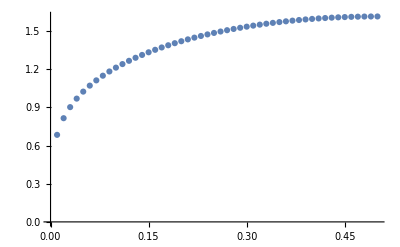

```mathematica
ListPlot[{(#[[1]])/200,(#[[2]])/200^2}&/@%365]
```

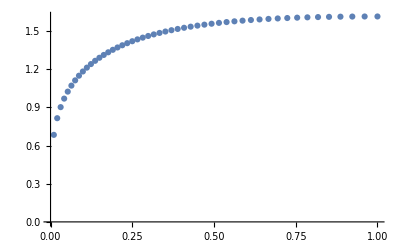

```mathematica
ListPlot[{(#[[1]])/(200-#[[1]]),(#[[2]])/200^2}&/@%365]
```

```mathematica
Jvector[{10,10},{p1,p2}][[1]].PseudoInverse[MMatrixN[{10,10}]].Jvector[{10,10},{p1,p2}][[1]]//FullSimplify
```

0.2459623807969 p1^2-0.4919247615938 p1 p2+0.2459623807969 p2^2

```mathematica
Jvector[{20,20},{p1,p2}][[1]].PseudoInverse[MMatrixN[{20,20}]].Jvector[{20,20},{p1,p2}][[1]]//FullSimplify
```

0.2332173830611 p1^2-0.4664347661221 p1 p2+0.2332173830611 p2^2

```mathematica
Jvector[{30,30},{p1,p2}][[1]].PseudoInverse[MMatrixN[{30,30}]].Jvector[{30,30},{p1,p2}][[1]]//FullSimplify
```

0.2290052887004 p1^2-0.4580105774008 p1 p2+0.2290052887004 p2^2

```mathematica
Jvector[{100,100},{p1,p2}][[1]].PseudoInverse[MMatrixN[{100,100}]].Jvector[{100,100},{p1,p2}][[1]]//FullSimplify
```

0.223138872598 p1^2-0.446277745196 p1 p2+0.223138872598 p2^2

```mathematica
0.05578471814947499614730876597528202376`14.68321513480475 * 2^2(p1-p2)^2//Expand
```

0.2231388725979 p1^2-0.4462777451958 p1 p2+0.2231388725979 p2^2

```mathematica
Jvector[{40,160},{p1,p2}][[1]].PseudoInverse[MMatrixN[{40,160}]].Jvector[{40,160},{p1,p2}][[1]]//FullSimplify
```

0.6471550598 p1^2-0.3235775299 p1 p2+0.04044719124 p2^2

```mathematica
0.02588620239180119311760031958400601025`14.69875937564892 * (200)^2(p1/40-p2/160)^2//Expand
```

0.64715505979503 p1^2-0.32357752989751 p1 p2+0.040447191237189 p2^2

```mathematica
Monitor[Table[{20n,RedJMJ[{10n,10n}]},{n,1,16}],n]
```

{{20,0.061490595199231},{40,0.058304345765266},{60,0.057251322175105},{80,0.056726512847629},{100,0.056412172342143},{120,0.056202839178113},{140,0.056053426770934},{160,0.05594142832674},{180,0.055854354493163},{200,0.055784718149475},{220,0.055727757983085},{240,0.05568030150685},{260,0.05564015336131},{280,0.055605746016265},{300,0.055575930312764},{320,0.055549844615697}}

```mathematica
Monitor[Table[{20n,RedJMJ[{4n,16n}]},{n,1,16}],n]
```

{{20,0.029576301433574},{40,0.027508154352279},{60,0.026828792791887},{80,0.026491010551635},{100,0.026288950337382},{120,0.026154497607835},{140,0.026058584460866},{160,0.025986717718187},{180,0.025930861737159},{200,0.025886202391801},{220,0.025849679748587},{240,0.025819255777984},{260,0.025793520630827},{280,0.025771467925356},{300,0.025752360054866},{320,0.025735644076401}}

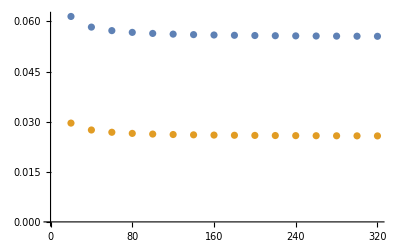

```mathematica
ListPlot[{%311,%313}]
```

```mathematica
103/80//N
```

1.2875

```mathematica
116/90//N
```

1.28889

```mathematica
128.796/100
```

1.28796

```mathematica
Det[RedMMatrixN[{40,50}]]/90
Times@@(MMatrixN[{40,50}]//Eigenvalues)[[;;-2]]
```

118.58334040331

118.5833404033

```mathematica
Det[RedMMatrixN[{40,60}]]
Times@@(MMatrixN[{40,60}]//Eigenvalues)[[;;-2]]
```

13414.972935948

134.1497293595

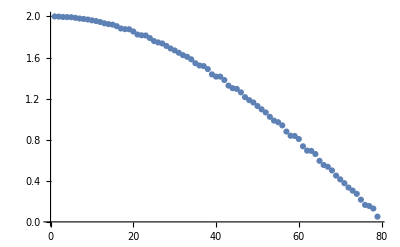

```mathematica
ListPlot[(MMatrixN[{44,36}]//Eigenvalues)[[;;-2]]]
```

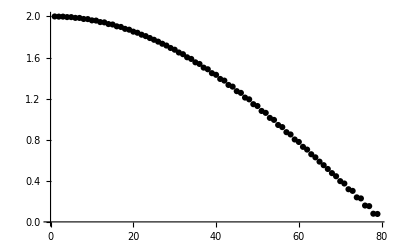

```mathematica
ListPlot[(MMatrixN[{2,78}]//Eigenvalues)[[;;-2]],PlotStyle->Black]
```

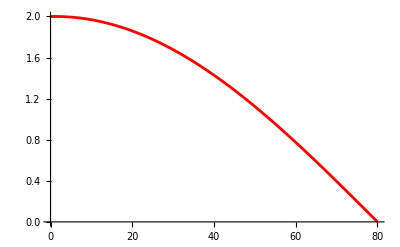

```mathematica
Plot[2Cos[Pi/2 (x-1)/79],{x,0,80},PlotStyle->Red]
```

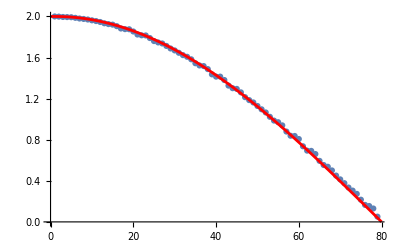

```mathematica
Show[%235,%250]
```

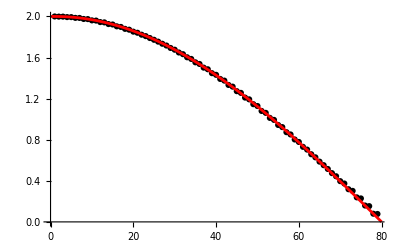

```mathematica
Show[%248,%250]
```

```mathematica
Table[{10n,Log[Times@@(MMatrixN[{4n,6n}]//Eigenvalues)[[;;-2]]]},{n,1,10}]
```

{{10,2.0196066191374},{20,2.8868852430187},{30,3.3938749279823},{40,3.753533067339},{50,4.032488243091},{60,4.260404176236},{70,4.453100962141},{80,4.620020679218},{90,4.767253228742},{100,4.898956559423}}

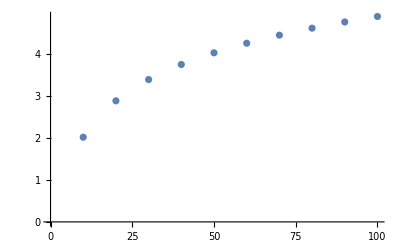

```mathematica
ListPlot[%228]
```

```mathematica
Table[{10n,Log[Times@@(MMatrixN[{2n,8n}]//Eigenvalues)[[;;-2]]]},{n,1,10}]
```

{{10,1.9012995253765},{20,2.7699536747184},{30,3.2772140052717},{40,3.636968211273},{50,3.915968095681},{60,4.143908380521},{70,4.336619872179},{80,4.503549142933},{90,4.650788246566},{100,4.782496267432}}

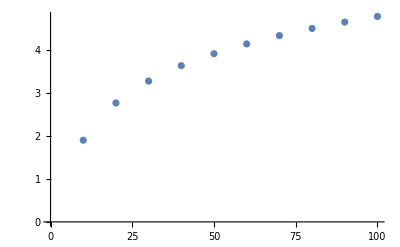

```mathematica
ListPlot[%231]
```